```mathematica
dataran=Flatten@Import["/home/LWang/data/Nbody/Ran2test/Ran2OUT","Table"];
```

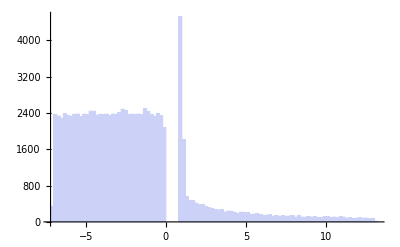

```mathematica
Histogram[Log10@dataran,100]
```

```mathematica
databin=Table[{(#[[1,i+1]]+#[[1,i]])/2,#[[2,i]]}&@HistogramList[Log@dataran],{i,1,Length[HistogramList[Log@dataran][[1]]]-1,1}];
```

FittedModel[1041.88 ({ | «1»)]

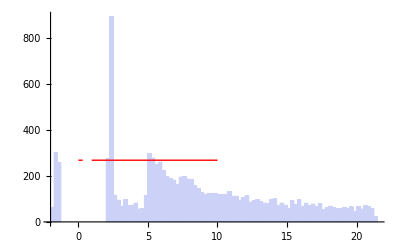

```mathematica
fitdataran=NonlinearModelFit[databin,b*D[fitdata[[4]][r],r],{b},r]
Histogram[Log@dataran,100,Epilog->First@Plot[fitdataran[x],{x,0,10},PlotRange->Full,PlotStyle->Red]]
```

```mathematica
ListPlot[xy,PlotStyle->PointSize[0.0000001],Joined->True]
```

-Graphics-

```mathematica
D[b*(1+r^-2)^(-3/2),r]
```

```mathematica
(3 b)/((1+1/r^2)^(5/2) r^3)-b
```

```mathematica
Simplify[+b+(3 b)/((1+1/r^2)^(5/2) r^3)]
```

b+(3 b)/((1+1/r^2)^(5/2) r^3)